```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}];
(*fileName = "~/Downloads/optimizerHistory.json";*)
```

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

```mathematica
runningBest = FoldList[Max,First[#],Rest[#]]&[raw[[All,"maximizeMe"]]];
```

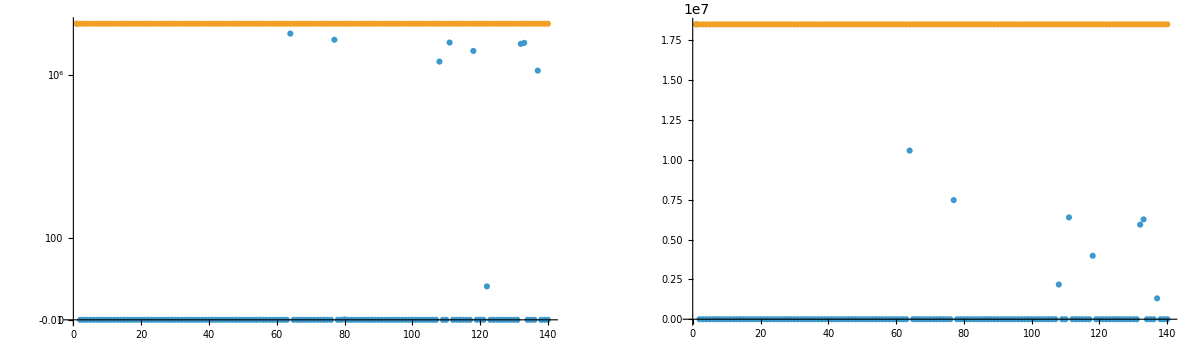

```mathematica
GraphicsGrid[{{
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -25.4393607728
L2PhaseSet : -38.7167888966
L1EnergyOffset : 1.0954646457512719e6
L2EnergyOffset : -4.3569233116633408e7
L3EnergyOffset : 4.2506806262124106e7
S1ELkG : 959.4476334417
S2ELkG : -3472.4668287239
S3ELkG : -964.7793337875
S1EL_xOffset : 0.0002888504
S1EL_yOffset : -0.0000220972
S2EL_xOffset : 0.000086259
S2EL_yOffset : -0.0000723185
S2ER_xOffset : 0.0000920866
S2ER_yOffset : -0.0000817839
S1ER_xOffset : 0.0001767671
S1ER_yOffset : -0.0000160852
XC1FFkG : 0.0094963765
XC3FFkG : -0.0036907044
YC1FFkG : -0.0011630606
YC2FFkG : 0.0019479112
PDrive_median_x : 5.8477e-6
PDrive_median_y : -9.5546e-6
PDrive_median_xp : -0.0000955039
PDrive_median_yp : -0.0000277693
PDrive_median_energy : 9.820243200984176636e9
PDrive_sigmaSI90_x : 0.0000198759
PDrive_sigmaSI90_y : 0.0000129893
PDrive_sigmaSI90_z : 4.546e-6
PDrive_fitSigma_x : 9.3099e-6
PDrive_fitSigma_y : 6.0928e-6
PDrive_fitSigma_z : 4.7126e-6
PDrive_sigmaSI90_xp : 0.0000538301
PDrive_sigmaSI90_yp : 0.0000298149
PDrive_sigmaSI90_energy : 7.724428899661088e7
PDrive_emitSI90_x : 0.0000102036
PDrive_emitSI90_y : 5.8525e-6
PDrive_norm_emit_x : 6.6474e-6
PDrive_norm_emit_y : 3.417e-6
PDrive_charge_nC : 1.59984
PDrive_BMAG_x : 2.063221868
PDrive_BMAG_y : 1.3738016137
PDrive_sliced_BMAG_x : List(6.2076058638,6.751110514,4.8541968192,2.8223339122,6.0339552297)
PDrive_sliced_BMAG_y : List(3.3986155641,2.9247129735,2.6656714652,1.8116703706,1.9706644277)
lostChargeFraction : 0.0001
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 4.867e-7
maximizeMe : 1.8492347518130291e7
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : False

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{L1PhaseSet,L2PhaseSet,L1EnergyOffset,L2EnergyOffset,L3EnergyOffset,S1ELkG,S2ELkG,S3ELkG,S1EL_xOffset,S1EL_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S1ER_xOffset,S1ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

## Plot specific

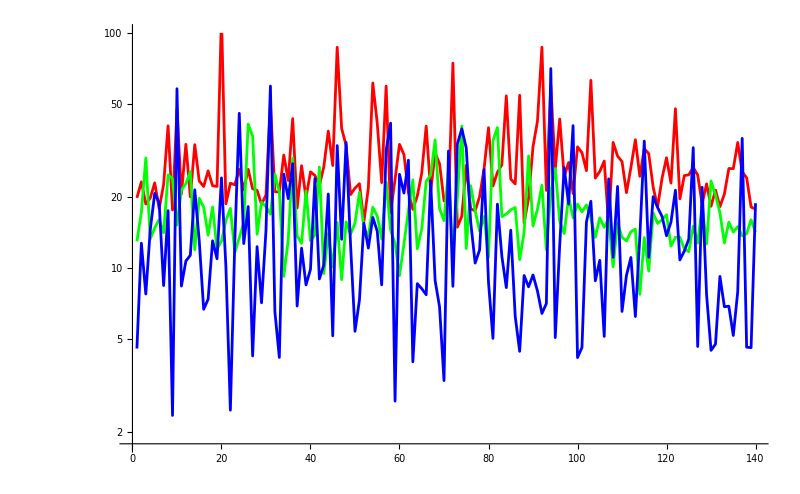

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

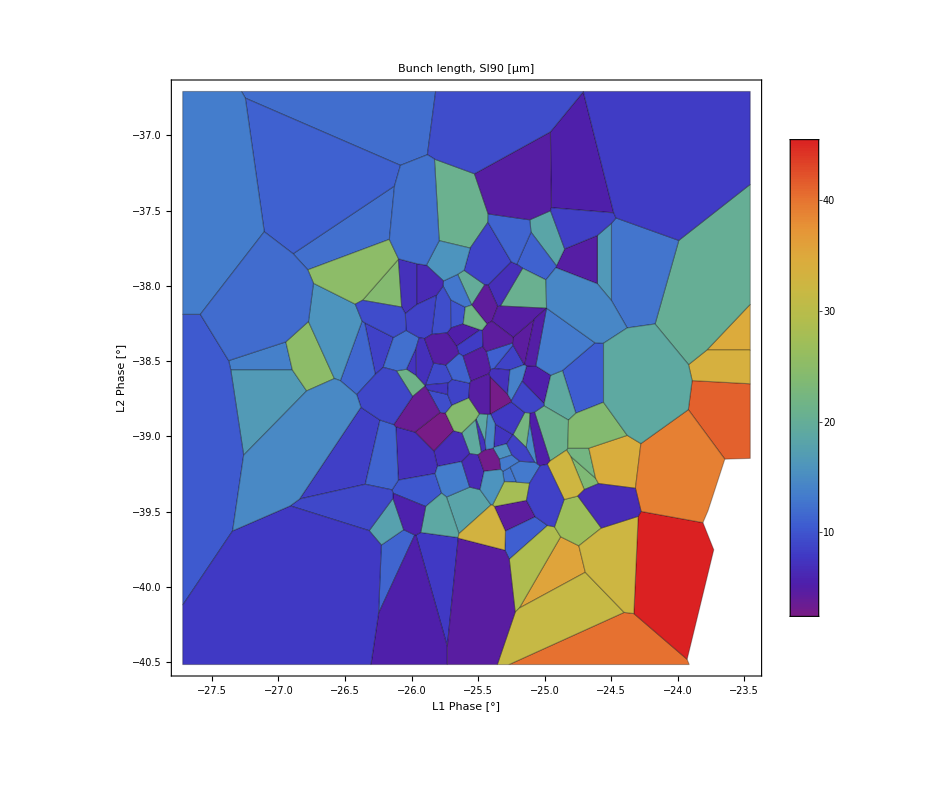

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,
PlotRange->{All,50},
(*PlotRange->{{-35,-21},{-50,-30},{All,50}},*)
Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"]&&MemberQ[Keys[raw[[1]]],"PWitness_sigmaSI90_z"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
]
```

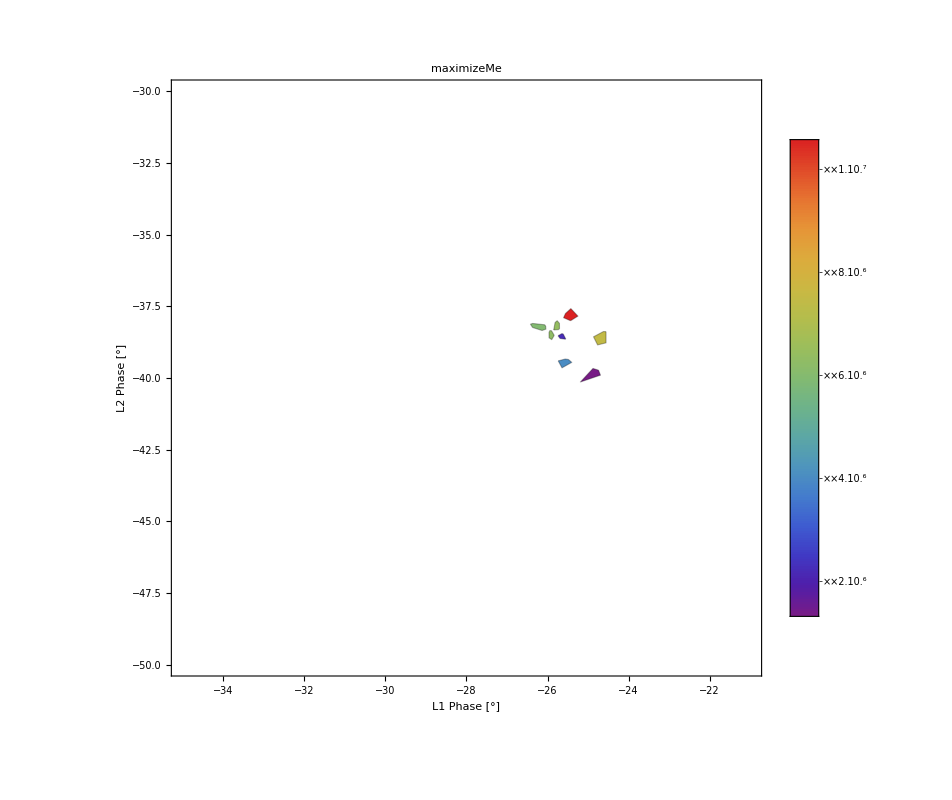

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
#["maximizeMe"]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",
InterpolationOrder->0,
(*PlotRange->{1*^5,All},*)
PlotRange->{{-35,-21},{-50,-30},{1*^5,All}},
Mesh->All,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"maximizeMe",LabelStyle->20]
]
```

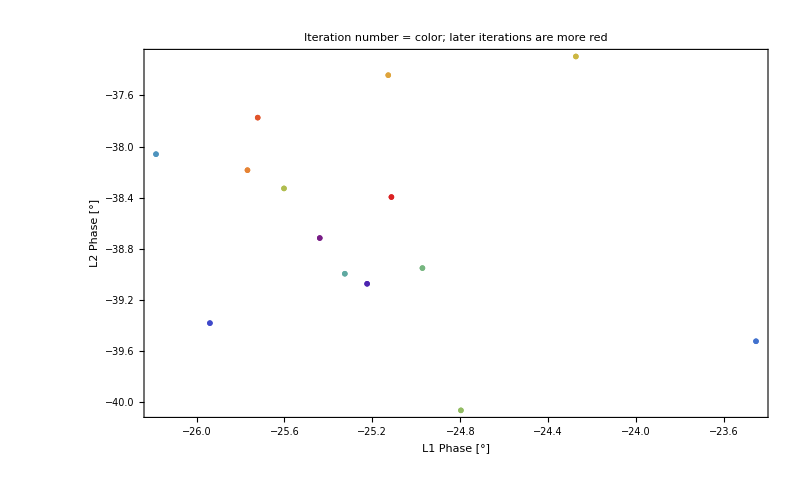

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]
]
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

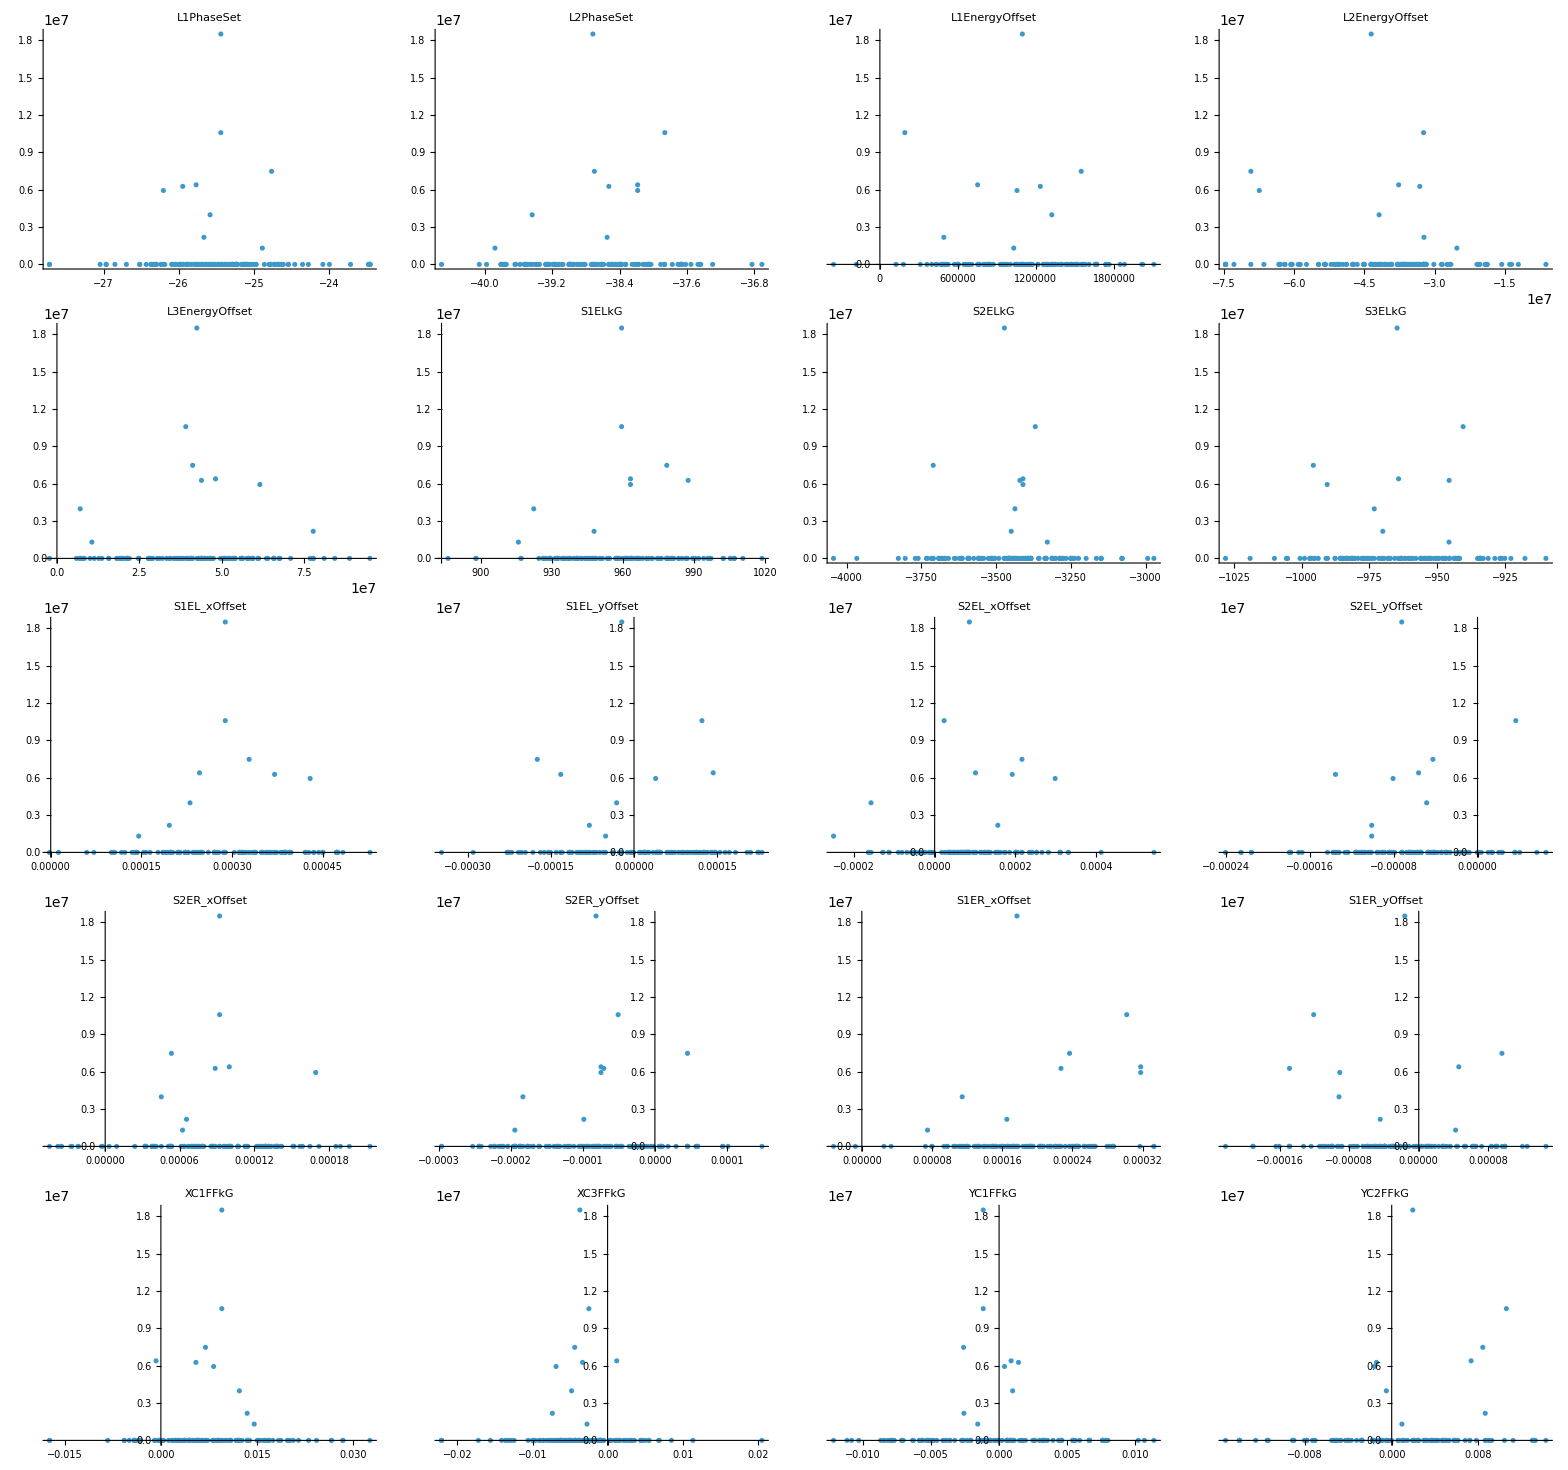

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

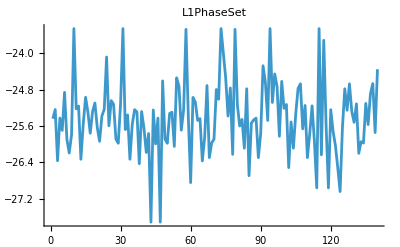
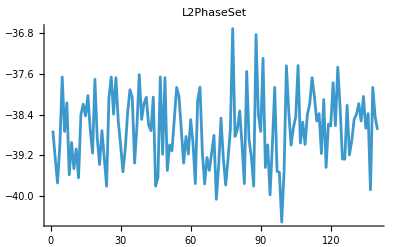
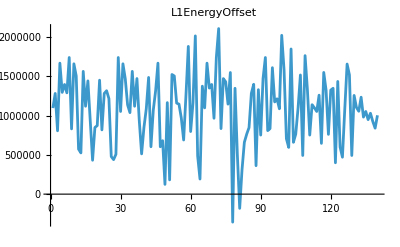
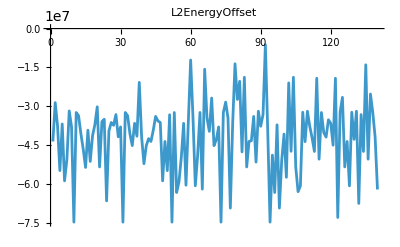
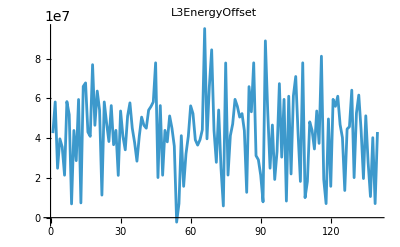
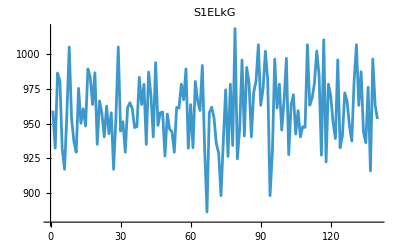
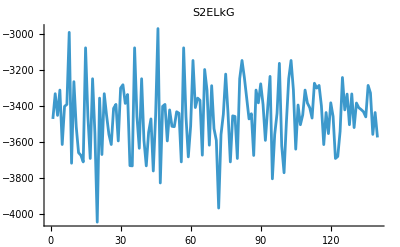
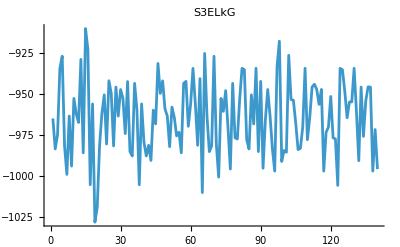
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Estimate maximizeMe asymptote

There’s no reason at all to think this is valid

```mathematica
(*runningBest = #["maximizeMe"]&/@raw;*)
```

```mathematica
Button["Calculate",

expr = a * Tanh[b ii]+c;
nlm=NonlinearModelFit[
Transpose[{Range[Length[runningBest]],runningBest}],
expr,
{
{a,Max[runningBest]},
{b,1/Length[runningBest]},
{c,Min[runningBest]}
},
ii,
Method->"NMinimize"
];

meanPredictionBands = nlm["MeanPredictionBands"];
singlePredictionBands = nlm["SinglePredictionBands"];
plotMe ={nlm["BestFit"]}~Join~meanPredictionBands~Join~singlePredictionBands;

img = Show[
ListPlot[
Transpose[{Range[Length[runningBest]],runningBest}],
PlotRange->{{0,Length[runningBest]*1.5},{0, Max[runningBest]*1.5}},
ImageSize->800
],

Plot[
plotMe,
{ii,0,Length[runningBest]*1.5},
PlotStyle->{{Opacity[0.5],Black},{Opacity[0.5],Red},{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Green}},
PlotRange->All
]

];

Print[
"Estimated limits: ",
Sort[
Limit[#,ii->Infinity]&/@plotMe
]
];
Print[img];
]
```

Calculate

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
(*Export[
"~/srData.csv",
Dataset[raw]
]*)
```

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{-25.4394,-38.7168,959.448,0.00028885,-0.0000220972,0.000176767,-0.0000160852,-3472.47,0.000086259,-0.0000723185,0.0000920866,-0.0000817839,-964.779,0.00949638,-0.0036907,-0.00116306,0.00194791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4607,-38.7232,959.585,0.000294897,-0.0000217409,0.000180866,-0.0000204817,-3441.14,0.0000818745,-0.0000642722,0.0000957999,-0.0000891598,-960.799,0.0109862,-0.00504371,-0.00152846,0.00258064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4893,-38.767,960.38,0.000280648,-0.0000252261,0.000173563,-0.0000119695,-3475.52,0.0000851323,-0.0000735925,0.0000844633,-0.0000717318,-964.779,0.0118161,-0.00391431,-0.00106085,0.00303966,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5263,-38.7514,956.289,0.000288529,-0.0000183508,0.000168487,-7.2414×10^-6,-3457.03,0.0000874136,-0.0000794058,0.0000837832,-0.0000752954,-964.853,0.00869429,-0.00293046,-0.00159363,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4566,-38.6982,962.238,0.0002918,-0.0000247946,0.000180815,-0.0000361284,-3465.39,0.0000825576,-0.0000790964,0.0000828143,-0.0000815935,-965.939,0.0105158,-0.00348707,-0.00156052,0.00181092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4732,-38.6654,962.03,0.00028378,-0.0000124045,0.000173601,-0.0000332718,-3460.29,0.0000753499,-0.0000807195,0.0000891243,-0.0000772856,-965.337,0.0105269,-0.00347884,-0.000324156,-0.0000171485,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4349,-38.6844,959.769,0.000287731,-0.0000315299,0.000193824,-0.0000189621,-3448.3,0.0000904616,-0.0000806683,0.0000928444,-0.0000703977,-964.044,0.00934983,-0.00337582,-0.00102219,0.00185653,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5759,-38.7198,962.092,0.000288909,-0.0000158898,0.00017587,-0.0000231015,-3483.42,0.0000855551,-0.0000787616,0.0000995581,-0.0000770811,-960.959,0.0102989,-0.0039431,-0.00149891,0.00253759,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7417,965.752,0.000293114,-0.0000189389,0.000173324,-0.0000140815,-3466.23,0.0000841415,-0.0000710489,0.0000862231,-0.0000821656,-964.699,0.0107329,-0.0036069,-0.00103874,0.0017983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5103,-38.7138,957.16,0.000283115,-0.0000321654,0.000176055,-0.0000324852,-3470.65,0.0000798764,-0.0000699889,0.0000943152,-0.0000793998,-964.585,0.00892456,-0.00411695,-0.00166668,0.00182661,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4485,-38.7691,958.551,0.000284839,-0.0000186597,0.000184183,-0.0000250236,-3457.25,0.000101521,-0.0000792881,0.000103865,-0.0000874858,-968.548,0.0105544,-0.00335058,-0.00157359,0.00233294,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4457,-38.7851,964.181,0.000293114,-0.0000275025,0.000171208,-3.8708×10^-6,-3466.23,0.0000837537,-0.0000710489,0.0000862231,-0.000077259,-964.699,0.0121246,-0.00358049,-0.000636931,0.00225881,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6345,-38.7615,965.619,0.000294897,-0.0000107711,0.000168789,-2.1327×10^-6,-3441.14,0.0000868909,-0.0000707419,0.000101581,-0.0000891598,-960.131,0.0105339,-0.0040252,-0.000982234,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4764,-38.6629,971.018,0.000288759,-0.0000134847,0.000178015,-0.0000379577,-3469.21,0.0000851323,-0.0000722539,0.0000911221,-0.0000839911,-965.143,0.0124138,-0.00391431,0.000125678,-0.000720279,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5211,-38.7514,966.047,0.000292087,-0.0000275909,0.000188969,-0.0000167203,-3444.06,0.0000879963,-0.0000787077,0.0000837832,-0.0000717217,-964.025,0.0105985,-0.00331808,-0.000909528,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4457,-38.7851,962.238,0.000285537,-0.0000275025,0.000180815,-3.8708×10^-6,-3465.39,0.0000837537,-0.0000663076,0.0000723775,-0.000077259,-968.203,0.0121246,-0.00348707,-0.000636931,0.00225881,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5706,-38.7127,971.076,0.000293463,-0.0000124045,0.000173601,-0.0000286291,-3490.43,0.0000824368,-0.0000704581,0.000100693,-0.0000838035,-961.127,0.0105269,-0.00453574,-0.000324156,-0.0000171485,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6883,-38.7998,959.769,0.000295955,-6.0759×10^-6,0.000162293,0.0000171007,-3448.3,0.0000881161,-0.0000633858,0.000103437,-0.0000703977,-959.372,0.0107496,-0.0041005,-0.000508316,0.00185653,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6038,-38.7646,971.536,0.000297025,-0.0000160419,0.000170166,-0.0000122436,-3460.5,0.0000821992,-0.0000787616,0.0000808449,-0.0000770811,-960.959,0.0118671,-0.00353004,-0.00149891,0.00166106,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5202,-38.7353,973.992,0.000297291,-0.000015742,0.000171243,-0.0000191516,-3472.47,0.0000812812,-0.0000634326,0.0000920866,-0.0000883317,-964.853,0.010942,-0.0036907,0.0000387937,0.00194791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,960.947,0.000280044,-0.0000321976,0.000176055,-0.0000231042,-3497.76,0.0000825284,-0.0000736636,0.0000943152,-0.0000793998,-968.962,0.011909,-0.00411695,-0.00166668,0.00182661,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3126,-38.6485,968.017,0.000289303,-0.0000361083,0.000190313,-0.0000629055,-3457.25,0.000079043,-0.0000792881,0.000103865,-0.0000924349,-970.722,0.0105544,-0.00304423,-0.00200386,0.00175646,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7417,969.271,0.000302684,-9.2314×10^-6,0.000170118,-0.0000140815,-3443.14,0.0000853225,-0.0000710489,0.0000977189,-0.0000938696,-964.699,0.00987181,-0.00368137,-0.00103874,0.00141226,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5833,-38.71,966.903,0.000294897,-0.0000107711,0.000174873,-2.1327×10^-6,-3441.14,0.0000844254,-0.0000745203,0.0000963602,-0.000085758,-962.133,0.0105339,-0.00362624,-0.000982234,0.00146113,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4893,-38.7266,963.794,0.000290543,-0.0000166975,0.000174908,-0.0000119695,-3478.29,0.0000849175,-0.0000735925,0.0000920025,-0.0000717318,-962.197,0.0118161,-0.0041744,-0.00106085,0.000478634,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.446,-38.6833,973.346,0.000291441,-0.0000231889,0.000180918,-0.000044792,-3494.52,0.0000803274,-0.0000757984,0.00008438,-0.0000752954,-965.878,0.0105834,-0.00293046,-0.00159363,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6154,-38.6982,962.238,0.000298812,-9.6398×10^-6,0.000168242,-3.4286×10^-6,-3438.88,0.0000874222,-0.0000749051,0.0000791502,-0.0000794093,-961.939,0.00857402,-0.0028101,-0.000989685,0.00240408,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5706,-38.7403,966.981,0.0002903,-0.0000233487,0.000166192,-0.0000286291,-3490.43,0.0000824368,-0.0000704581,0.0000731933,-0.0000715859,-962.168,0.0115802,-0.00398548,-0.000694403,0.0022729,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4857,-38.7137,963.384,0.000289093,-0.0000223764,0.000162293,-0.0000281634,-3494.62,0.0000881161,-0.0000764347,0.0000848645,-0.000074054,-959.372,0.010575,-0.0041005,-0.00138572,0.00184716,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6226,-38.738,969.271,0.000302684,-9.2314×10^-6,0.00017587,-7.4755×10^-6,-3443.14,0.0000853225,-0.0000787616,0.0000995581,-0.0000770811,-960.959,0.00987181,-0.00368137,-0.000985946,0.00141226,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5197,-38.7353,963.276,0.000288439,-0.000015742,0.000175586,-0.0000191516,-3472.47,0.0000968764,-0.0000634326,0.00010036,-0.0000861227,-964.853,0.0107589,-0.0036907,0.0000387937,0.00194791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,966.163,0.000282834,-0.0000317994,0.000180893,-0.000033604,-3484.5,0.0000821377,-0.0000736636,0.0000943152,-0.0000830616,-968.962,0.0114492,-0.00411695,-0.00166668,0.00259284,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4485,-38.7629,961.855,0.000292859,-0.0000186597,0.000168366,-3.4304×10^-6,-3448.51,0.0000853896,-0.0000714815,0.000103865,-0.0000809664,-968.548,0.00965533,-0.00292685,-0.00157359,0.00233294,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6028,-38.7444,963.062,0.000293114,-0.0000109395,0.000168952,-4.9176×10^-6,-3442.7,0.0000841415,-0.0000710489,0.0000801388,-0.0000797945,-964.699,0.0107329,-0.0036069,-0.000996542,0.00231941,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5223,-38.738,970.513,0.000295527,-0.000017092,0.000172122,-2.1327×10^-6,-3441.14,0.0000824891,-0.000066649,0.0000896104,-0.0000891598,-964.788,0.0105339,-0.00365531,-0.00041625,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7783,967.706,0.000294904,-0.0000108375,0.000166376,-0.0000119695,-3475.52,0.0000866448,-0.0000662225,0.0000844633,-0.0000717318,-964.779,0.0118161,-0.00391778,-0.000704667,0.00217606,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5223,-38.7514,956.289,0.000295527,-0.000017092,0.000172122,-7.2414×10^-6,-3457.03,0.0000824891,-0.000066649,0.0000837832,-0.0000857278,-964.788,0.00869429,-0.00293046,-0.00041625,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4837,-38.7613,956.832,0.00028592,-0.0000206244,0.0001808,-0.0000174737,-3457.44,0.0000958338,-0.0000790964,0.0000828143,-0.0000815935,-965.939,0.010509,-0.00341041,-0.00197021,0.00202073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5706,-38.7328,966.981,0.000288272,-0.0000233487,0.000175997,-0.0000163634,-3490.43,0.0000866105,-0.0000799045,0.0000905394,-0.0000715859,-962.449,0.0103613,-0.00375271,-0.00192707,0.00213895,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4825,-38.7998,967.059,0.000286939,-0.0000198445,0.000162293,0.0000171007,-3466.35,0.000095136,-0.0000633858,0.0000978246,-0.0000703977,-966.871,0.0107496,-0.0038496,-0.000508316,0.00185653,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5694,-38.7259,969.913,0.000297895,-0.0000191001,0.000167051,-7.7603×10^-6,-3471.41,0.0000741015,-0.0000662892,0.0000760312,-0.0000790922,-962.475,0.0102989,-0.00375498,-0.00149891,0.00148943,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7353,964.477,0.000291386,-0.000015742,0.000172934,-0.0000165132,-3468.6,0.0000913877,-0.0000710104,0.0000910943,-0.0000779135,-966.03,0.0116094,-0.00370095,-0.000579907,0.00219496,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4641,-38.7468,959.157,0.000293475,-0.0000225521,0.000176643,-0.0000113501,-3455.55,0.0000817407,-0.0000712953,0.0000858302,-0.0000793998,-968.962,0.00892941,-0.00303653,-0.000872122,0.00211754,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5507,-38.7691,968.156,0.000295876,-0.0000186597,0.0001697,-0.0000104297,-3469.22,0.000101521,-0.0000682992,0.0000803352,-0.0000874858,-968.548,0.0104822,-0.00335058,-0.00130458,0.00161987,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7771,965.752,0.000284554,-0.0000243298,0.000169858,-4.5972×10^-6,-3489.8,0.0000841202,-0.0000670928,0.0000945981,-0.0000805682,-966.901,0.0117474,-0.00406558,-0.00111605,0.00180973,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6,-38.7684,967.175,0.000294417,-0.0000130394,0.000168265,-0.0000125435,-3441.14,0.0000859644,-0.0000675343,0.0000849416,-0.0000745677,-964.758,0.0115217,-0.00383329,-0.000982234,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7498,957.967,0.000296921,-0.0000143827,0.000166376,1.4931×10^-6,-3441.91,0.0000841796,-0.0000682751,0.0000939347,-0.0000717318,-966.607,0.00863135,-0.00283863,-0.000704667,0.00213019,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.575,-38.7734,956.289,0.000294071,-0.0000146747,0.000167869,1.9731×10^-6,-3466.84,0.0000852949,-0.000066649,0.0000887054,-0.0000825823,-963.796,0.00869429,-0.00369417,-0.000658782,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4566,-38.7223,969.144,0.0002829,-0.0000316991,0.000179285,-0.0000323429,-3465.39,0.000082127,-0.000076157,0.0000903082,-0.0000798482,-968.461,0.0130739,-0.00348707,-0.0017727,0.00182561,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4506,-38.7147,964.122,0.0002903,-0.000025531,0.000179063,-0.0000283654,-3463.89,0.0000824368,-0.0000769372,0.0000801936,-0.0000715859,-964.633,0.00993649,-0.00345115,-0.000694403,0.0022729,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7998,959.79,0.00029507,-6.0759×10^-6,0.000162293,-6.197×10^-7,-3464.94,0.0000797046,-0.0000678729,0.0000844835,-0.0000703977,-959.372,0.0107496,-0.0041005,-0.000508316,0.00150275,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5134,-38.7139,971.715,0.000291159,-0.0000191001,0.000167051,-0.0000275433,-3467.51,0.0000741015,-0.000074225,0.0000879627,-0.0000787659,-966.326,0.0128557,-0.00361184,-0.00149891,0.00209384,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7684,967.175,0.000294417,-0.0000130394,0.000168265,-0.0000165132,-3472.99,0.0000913877,-0.0000675343,0.0000849416,-0.0000745677,-964.758,0.0116094,-0.00383329,-0.000795467,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5006,-38.7468,960.516,0.000280044,-6.3608×10^-6,0.000170485,-0.0000231042,-3447.67,0.0000821519,-0.0000691664,0.0000943152,-0.0000813004,-962.663,0.011909,-0.00369066,-0.000903231,0.00123747,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7407,966.647,0.000291065,-0.0000221501,0.0001697,-0.0000104297,-3483.85,0.000101521,-0.0000706187,0.0000803352,-0.0000874858,-962.856,0.0104822,-0.00388258,-0.000787993,0.0021439,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4967,-38.7417,959.612,0.000292667,-0.0000210026,0.000174127,-6.5827×10^-6,-3466.23,0.0000841415,-0.0000710489,0.0000885047,-0.0000880014,-964.17,0.00905386,-0.0036069,-0.00101406,0.0017983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5804,-38.7614,966.803,0.000294077,-0.0000107711,0.000168789,-2.1327×10^-6,-3441.14,0.0000868909,-0.0000684531,0.0000852766,-0.0000891598,-960.131,0.0113155,-0.0040252,-0.000982234,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7783,966.305,0.000291053,-0.0000250589,0.000166376,-0.0000185439,-3489.2,0.0000920099,-0.0000662225,0.0000747963,-0.0000812653,-966.164,0.010705,-0.00391778,-0.000934272,0.00162569,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.556,-38.7734,966.142,0.000294071,-0.0000122099,0.000173423,1.9731×10^-6,-3466.84,0.0000864047,-0.0000687709,0.0000887054,-0.0000822441,-963.796,0.0108598,-0.00369417,-0.000658782,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4472,-38.7132,962.238,0.000285033,-0.000032988,0.000180815,-0.0000361284,-3483.88,0.0000856602,-0.0000741634,0.0000915109,-0.0000870073,-969.857,0.0113565,-0.00361575,-0.00166175,0.00181092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4845,-38.7454,966.589,0.000292856,-0.0000201588,0.000166192,-0.0000286291,-3483.36,0.0000824368,-0.0000693238,0.0000731933,-0.0000743175,-962.168,0.0113113,-0.00398548,-0.000938292,0.00158776,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4943,-38.7213,965.363,0.000290638,-6.0759×10^-6,0.000173225,-0.0000230416,-3474.25,0.0000818783,-0.0000678729,0.0000844835,-0.0000703977,-963.295,0.0107496,-0.0041005,-0.00103322,0.00150275,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6133,-38.756,969.913,0.000300659,-8.1888×10^-6,0.000167051,-7.7603×10^-6,-3471.41,0.0000862263,-0.0000684175,0.0000760312,-0.0000836954,-962.475,0.0102989,-0.00337952,-0.00149891,0.00177812,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5216,-38.7507,966.875,0.000293118,-0.0000189746,0.000172027,-0.0000193721,-3484.72,0.0000913877,-0.0000675343,0.0000849416,-0.0000727923,-967.199,0.0116094,-0.00354913,-0.000795467,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,968.959,0.000292063,-0.000025857,0.000179257,-0.0000213217,-3466.92,0.0000865278,-0.0000727571,0.0000871587,-0.0000884948,-968.962,0.0107239,-0.00334143,-0.00132402,0.00195725,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7407,962.117,0.000285122,-0.000030427,0.00017853,-0.0000200701,-3478.19,0.0000819276,-0.000075051,0.0000803352,-0.0000862897,-966.949,0.0107828,-0.00371402,-0.00155614,0.00161035,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4949,-38.7417,959.302,0.000297393,-3.4448×10^-6,0.000169826,0.0000110435,-3443.36,0.0000816907,-0.0000687299,0.0000963506,-0.0000810998,-964.699,0.0107329,-0.00371008,-0.000871816,0.00110745,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5271,-38.7124,962.142,0.000294897,-0.00003528,0.000177905,-0.0000338548,-3476.41,0.0000801254,-0.0000766823,0.0000787149,-0.0000857946,-960.131,0.0106639,-0.00362471,-0.0018437,0.00163795,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5956,-38.7783,965.283,0.000293855,-0.0000108375,0.000169167,-0.0000177645,-3475.52,0.0000845776,-0.0000728169,0.0000844633,-0.0000883691,-961.412,0.0118161,-0.00391778,-0.00132888,0.00217606,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5157,-38.7734,963.296,0.000294071,-0.0000122099,0.000174413,1.9731×10^-6,-3467.65,0.0000996476,-0.0000687709,0.000094216,-0.000078107,-966.746,0.0108598,-0.00369417,-0.000407735,0.00232212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5225,-38.7132,962.238,0.000292804,-0.0000181948,0.000177951,-0.0000361284,-3460.7,0.0000856602,-0.0000721582,0.0000915109,-0.0000890516,-969.857,0.0100604,-0.00361575,-0.000916131,0.00154329,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4056,-38.7463,961.442,0.0002903,-0.0000308323,0.000175774,-0.0000221751,-3490.43,0.0000824368,-0.0000733944,0.0000731933,-0.0000796847,-968.523,0.0115802,-0.00406442,-0.00160202,0.0018237,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7178,959.79,0.00029507,-0.0000368683,0.000175685,-0.0000365764,-3464.94,0.0000806644,-0.0000754378,0.0000844835,-0.0000796142,-969.333,0.0116741,-0.00398615,-0.00194285,0.00183194,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.363,-38.6833,969.913,0.00028426,-0.0000388083,0.000186276,-7.7603×10^-6,-3471.41,0.0000832583,-0.0000781721,0.000092545,-0.0000958681,-969.254,0.0103206,-0.00333597,-0.00189726,0.00147076,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7761,967.175,0.000293269,-0.0000130394,0.000168265,-0.0000127243,-3487.58,0.0000776952,-0.0000684754,0.000070886,-0.0000653356,-964.018,0.0109263,-0.00367445,-0.000613625,0.00093529,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,965.633,0.000294714,-0.0000116122,0.000169256,-3.3632×10^-6,-3443.72,0.0000866078,-0.0000707735,0.0000943152,-0.0000884395,-968.962,0.0105544,-0.00411695,-0.000988052,0.00239619,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7798,963.296,0.000289995,-0.0000135023,0.000174413,-0.0000219331,-3478.19,0.0000996476,-0.0000721659,0.000094216,-0.000078107,-966.949,0.0119085,-0.00367715,-0.000407735,0.00232212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4361,-38.6978,965.752,0.000285638,-0.0000189389,0.000183323,-0.0000140815,-3474.9,0.0000841415,-0.0000763302,0.0000862231,-0.0000821656,-968.762,0.0107329,-0.0036069,-0.00172889,0.00158919,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6582,-38.7615,970.714,0.000304565,-3.6758×10^-6,0.000168789,-8.8305×10^-6,-3441.14,0.0000911995,-0.0000707419,0.000101581,-0.0000783159,-961.349,0.0104942,-0.00338091,-0.000982234,0.0019949,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7783,969.581,0.000303527,-8.3758×10^-6,0.000166376,-6.8932×10^-6,-3441.11,0.0000854266,-0.0000689658,0.0000797763,-0.0000843691,-961.302,0.00979592,-0.00320056,-0.000538469,0.00177574,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4785,-38.7734,967.511,0.000295498,-0.0000255216,0.000173423,-0.0000107281,-3462.95,0.0000741484,-0.000071102,0.0000795053,-0.0000822441,-963.796,0.00952409,-0.0034772,-0.0016715,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5977,-38.7132,972.059,0.000292982,-0.0000227323,0.000176577,-0.0000231237,-3474.65,0.0000896706,-0.0000697341,0.000086207,-0.0000870073,-969.007,0.0115826,-0.00361575,-0.00166175,0.00233471,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5515,-38.7721,963.796,0.000290629,-0.0000146076,0.000174192,-0.0000286291,-3475.76,0.000096495,-0.0000704581,0.0000925909,-0.0000715859,-962.168,0.0116695,-0.00366286,-0.000694403,0.0022729,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7114,967.709,0.0002956,-0.0000232701,0.000172457,-7.8263×10^-6,-3464.94,0.000071788,-0.0000701591,0.0000798553,-0.0000703977,-962.907,0.0097963,-0.00355094,-0.00154145,0.00138098,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5694,-38.7469,960.945,0.000284944,-0.0000259887,0.000181182,-9.6799×10^-6,-3472.07,0.0000842145,-0.0000662892,0.000103051,-0.0000883909,-970.112,0.0109948,-0.00371164,-0.00149891,0.00144275,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7684,968.688,0.000293358,-0.0000267833,0.000166775,-0.0000165132,-3475.98,0.0000704299,-0.0000696884,0.0000694747,-0.0000769703,-964.758,0.0104713,-0.00383329,-0.00126713,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.534,-38.7468,971.024,0.000299409,-0.0000233986,0.000167459,-2.7902×10^-6,-3497.76,0.0000637893,-0.0000736636,0.0000717355,-0.0000829505,-961.135,0.011909,-0.00366891,-0.00190807,0.00113491,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4942,-38.7856,963.296,0.000294258,-0.0000135023,0.000166702,-8.815×10^-6,-3464.9,0.0000855095,-0.0000692964,0.000085215,-0.0000722552,-961.314,0.0107543,-0.00378021,-0.000348586,0.00232212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7316,965.752,0.000298436,-0.0000189389,0.000173926,5.407×10^-7,-3452.9,0.0000783012,-0.0000681279,0.0000882115,-0.0000874251,-964.699,0.00983508,-0.0034454,-0.00103874,0.00124934,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6345,-38.7788,957.881,0.000290074,-6.8013×10^-6,0.000169705,-0.0000125607,-3443.23,0.0000952929,-0.0000669915,0.0000951553,-0.0000733702,-960.131,0.00992051,-0.00390931,-0.0000579743,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7182,966.478,0.000288611,-0.0000108375,0.000166376,-0.0000283286,-3450.04,0.000102276,-0.0000682956,0.0000963629,-0.0000717318,-964.779,0.0105042,-0.00356965,-0.000704667,0.00217606,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.556,-38.715,966.142,0.0002953,-0.0000227481,0.000173423,1.9731×10^-6,-3457.85,0.0000732768,-0.0000702663,0.0000806227,-0.0000850094,-963.123,0.0108598,-0.00355769,-0.000658782,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5786,-38.7289,972.059,0.00029655,-0.0000227323,0.000176577,-2.08×10^-7,-3440.27,0.0000752032,-0.0000700512,0.000086207,-0.00008991,-969.007,0.00976976,-0.00361575,-0.00166175,0.00233471,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5405,-38.7604,966.981,0.000289375,-0.0000110993,0.000166192,-0.0000107439,-3444.56,0.0000999875,-0.0000676207,0.0000731933,-0.0000816707,-962.168,0.0115802,-0.0036246,-0.000163402,0.00225667,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7998,959.79,0.000294456,-0.0000105579,0.000162293,6.263×10^-7,-3442.75,0.0000821938,-0.0000678729,0.0000969954,-0.0000836738,-958.48,0.0099981,-0.0041005,-0.000562624,0.00188946,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5694,-38.7259,969.913,0.000297895,-0.0000208525,0.000167051,-0.0000279551,-3471.41,0.0000741015,-0.0000662892,0.0000810625,-0.0000744213,-969.476,0.0102989,-0.00375498,-0.000636206,0.00148943,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5479,-38.7684,972.846,0.000295094,-0.0000280645,0.000176658,-0.0000190847,-3470.76,0.0000802155,-0.0000699393,0.0000849416,-0.0000882576,-966.873,0.0116094,-0.0033648,-0.000795467,0.00178896,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.534,-38.7151,965.245,0.000299409,-0.0000233986,0.000167459,-0.0000257544,-3476.67,0.000081193,-0.0000736636,0.0000717355,-0.0000829505,-962.869,0.0105676,-0.00366891,-0.00103155,0.00186615,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5463,-38.7873,963.296,0.000289995,-0.0000106045,0.000166177,-6.266×10^-6,-3478.19,0.0000820214,-0.0000721659,0.0000850013,-0.0000714625,-961.737,0.0119085,-0.00367715,-0.00036814,0.00168713,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5527,-38.7417,967.846,0.000293114,-0.0000189389,0.000182617,-0.0000140815,-3469.39,0.0000841415,-0.0000744093,0.0000961491,-0.0000821656,-971.07,0.0119851,-0.00347109,-0.00103874,0.0017983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5037,-38.7615,965.619,0.00029832,-0.0000107711,0.000167506,-0.0000411281,-3475.82,0.0000868909,-0.0000758215,0.00006967,-0.0000891598,-963.795,0.0105339,-0.00358227,-0.000982234,0.00187345,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4866,-38.7783,957.205,0.000294904,-9.9355×10^-6,0.000171213,-0.0000129201,-3469.67,0.0000938734,-0.0000662225,0.0000940354,-0.000073484,-962.691,0.0110508,-0.00366679,0.000184476,0.00178601,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5316,-38.7254,966.142,0.000293108,-0.0000122099,0.000173423,-4.4863×10^-6,-3432.69,0.0000843815,-0.0000754573,0.000102921,-0.0000991656,-960.165,0.00948218,-0.00369417,-0.00130949,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4507,-38.7596,963.487,0.000288332,-0.000021603,0.00017881,-0.0000333956,-3502.36,0.0000965849,-0.0000724379,0.000086207,-0.0000870073,-971.349,0.0115826,-0.0032674,-0.000478351,0.00165909,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4578,-38.732,965.235,0.00029264,-0.0000210867,0.000175166,-0.0000185136,-3463.76,0.0000887679,-0.0000704581,0.0000731933,-0.0000849319,-962.168,0.0115802,-0.00352448,-0.00112731,0.00169814,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5263,-38.7558,962.892,0.000285706,-0.000023083,0.000172486,-0.0000344378,-3464.94,0.000092272,-0.0000751155,0.000083455,-0.0000748436,-959.372,0.0119828,-0.0041005,-0.00025399,0.00256252,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4808,-38.7259,964.554,0.00029586,-0.0000191001,0.000180281,1.088×10^-7,-3442.62,0.0000741015,-0.0000662892,0.0000989329,-0.0000924856,-967.168,0.00990638,-0.00323762,-0.00137462,0.00133535,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4627,-38.7684,967.081,0.00028863,-0.0000130394,0.000170791,-0.0000399272,-3514.3,0.0000797968,-0.0000675343,0.0000585324,-0.0000650233,-966.686,0.0117535,-0.00356816,-0.000757979,0.00161108,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.512,-38.7151,962.074,0.000289384,-0.0000122179,0.00017954,-4.5871×10^-6,-3461.76,0.000081193,-0.0000734697,0.0000717355,-0.0000852402,-962.869,0.0112801,-0.00354758,-0.000219243,0.00209061,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7211,967.081,0.000289995,-0.0000312075,0.000170791,-0.0000399272,-3514.3,0.0000797968,-0.0000721659,0.000094216,-0.0000650233,-966.949,0.0119085,-0.00367715,-0.000757979,0.00161108,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{-25.4394,-38.7168,959.448,0.00028885,-0.0000220972,0.000176767,-0.0000160852,-3472.47,0.000086259,-0.0000723185,0.0000920866,-0.0000817839,-964.779,0.00949638,-0.0036907,-0.00116306,0.00194791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4607,-38.7232,959.585,0.000294897,-0.0000217409,0.000180866,-0.0000204817,-3441.14,0.0000818745,-0.0000642722,0.0000957999,-0.0000891598,-960.799,0.0109862,-0.00504371,-0.00152846,0.00258064,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4893,-38.767,960.38,0.000280648,-0.0000252261,0.000173563,-0.0000119695,-3475.52,0.0000851323,-0.0000735925,0.0000844633,-0.0000717318,-964.779,0.0118161,-0.00391431,-0.00106085,0.00303966,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5263,-38.7514,956.289,0.000288529,-0.0000183508,0.000168487,-7.2414×10^-6,-3457.03,0.0000874136,-0.0000794058,0.0000837832,-0.0000752954,-964.853,0.00869429,-0.00293046,-0.00159363,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4566,-38.6982,962.238,0.0002918,-0.0000247946,0.000180815,-0.0000361284,-3465.39,0.0000825576,-0.0000790964,0.0000828143,-0.0000815935,-965.939,0.0105158,-0.00348707,-0.00156052,0.00181092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4732,-38.6654,962.03,0.00028378,-0.0000124045,0.000173601,-0.0000332718,-3460.29,0.0000753499,-0.0000807195,0.0000891243,-0.0000772856,-965.337,0.0105269,-0.00347884,-0.000324156,-0.0000171485,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4349,-38.6844,959.769,0.000287731,-0.0000315299,0.000193824,-0.0000189621,-3448.3,0.0000904616,-0.0000806683,0.0000928444,-0.0000703977,-964.044,0.00934983,-0.00337582,-0.00102219,0.00185653,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5759,-38.7198,962.092,0.000288909,-0.0000158898,0.00017587,-0.0000231015,-3483.42,0.0000855551,-0.0000787616,0.0000995581,-0.0000770811,-960.959,0.0102989,-0.0039431,-0.00149891,0.00253759,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7417,965.752,0.000293114,-0.0000189389,0.000173324,-0.0000140815,-3466.23,0.0000841415,-0.0000710489,0.0000862231,-0.0000821656,-964.699,0.0107329,-0.0036069,-0.00103874,0.0017983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5103,-38.7138,957.16,0.000283115,-0.0000321654,0.000176055,-0.0000324852,-3470.65,0.0000798764,-0.0000699889,0.0000943152,-0.0000793998,-964.585,0.00892456,-0.00411695,-0.00166668,0.00182661,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4485,-38.7691,958.551,0.000284839,-0.0000186597,0.000184183,-0.0000250236,-3457.25,0.000101521,-0.0000792881,0.000103865,-0.0000874858,-968.548,0.0105544,-0.00335058,-0.00157359,0.00233294,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4457,-38.7851,964.181,0.000293114,-0.0000275025,0.000171208,-3.8708×10^-6,-3466.23,0.0000837537,-0.0000710489,0.0000862231,-0.000077259,-964.699,0.0121246,-0.00358049,-0.000636931,0.00225881,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6345,-38.7615,965.619,0.000294897,-0.0000107711,0.000168789,-2.1327×10^-6,-3441.14,0.0000868909,-0.0000707419,0.000101581,-0.0000891598,-960.131,0.0105339,-0.0040252,-0.000982234,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4764,-38.6629,971.018,0.000288759,-0.0000134847,0.000178015,-0.0000379577,-3469.21,0.0000851323,-0.0000722539,0.0000911221,-0.0000839911,-965.143,0.0124138,-0.00391431,0.000125678,-0.000720279,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5211,-38.7514,966.047,0.000292087,-0.0000275909,0.000188969,-0.0000167203,-3444.06,0.0000879963,-0.0000787077,0.0000837832,-0.0000717217,-964.025,0.0105985,-0.00331808,-0.000909528,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4457,-38.7851,962.238,0.000285537,-0.0000275025,0.000180815,-3.8708×10^-6,-3465.39,0.0000837537,-0.0000663076,0.0000723775,-0.000077259,-968.203,0.0121246,-0.00348707,-0.000636931,0.00225881,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5706,-38.7127,971.076,0.000293463,-0.0000124045,0.000173601,-0.0000286291,-3490.43,0.0000824368,-0.0000704581,0.000100693,-0.0000838035,-961.127,0.0105269,-0.00453574,-0.000324156,-0.0000171485,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6883,-38.7998,959.769,0.000295955,-6.0759×10^-6,0.000162293,0.0000171007,-3448.3,0.0000881161,-0.0000633858,0.000103437,-0.0000703977,-959.372,0.0107496,-0.0041005,-0.000508316,0.00185653,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6038,-38.7646,971.536,0.000297025,-0.0000160419,0.000170166,-0.0000122436,-3460.5,0.0000821992,-0.0000787616,0.0000808449,-0.0000770811,-960.959,0.0118671,-0.00353004,-0.00149891,0.00166106,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5202,-38.7353,973.992,0.000297291,-0.000015742,0.000171243,-0.0000191516,-3472.47,0.0000812812,-0.0000634326,0.0000920866,-0.0000883317,-964.853,0.010942,-0.0036907,0.0000387937,0.00194791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,960.947,0.000280044,-0.0000321976,0.000176055,-0.0000231042,-3497.76,0.0000825284,-0.0000736636,0.0000943152,-0.0000793998,-968.962,0.011909,-0.00411695,-0.00166668,0.00182661,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3126,-38.6485,968.017,0.000289303,-0.0000361083,0.000190313,-0.0000629055,-3457.25,0.000079043,-0.0000792881,0.000103865,-0.0000924349,-970.722,0.0105544,-0.00304423,-0.00200386,0.00175646,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7417,969.271,0.000302684,-9.2314×10^-6,0.000170118,-0.0000140815,-3443.14,0.0000853225,-0.0000710489,0.0000977189,-0.0000938696,-964.699,0.00987181,-0.00368137,-0.00103874,0.00141226,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5833,-38.71,966.903,0.000294897,-0.0000107711,0.000174873,-2.1327×10^-6,-3441.14,0.0000844254,-0.0000745203,0.0000963602,-0.000085758,-962.133,0.0105339,-0.00362624,-0.000982234,0.00146113,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4893,-38.7266,963.794,0.000290543,-0.0000166975,0.000174908,-0.0000119695,-3478.29,0.0000849175,-0.0000735925,0.0000920025,-0.0000717318,-962.197,0.0118161,-0.0041744,-0.00106085,0.000478634,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.446,-38.6833,973.346,0.000291441,-0.0000231889,0.000180918,-0.000044792,-3494.52,0.0000803274,-0.0000757984,0.00008438,-0.0000752954,-965.878,0.0105834,-0.00293046,-0.00159363,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6154,-38.6982,962.238,0.000298812,-9.6398×10^-6,0.000168242,-3.4286×10^-6,-3438.88,0.0000874222,-0.0000749051,0.0000791502,-0.0000794093,-961.939,0.00857402,-0.0028101,-0.000989685,0.00240408,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5706,-38.7403,966.981,0.0002903,-0.0000233487,0.000166192,-0.0000286291,-3490.43,0.0000824368,-0.0000704581,0.0000731933,-0.0000715859,-962.168,0.0115802,-0.00398548,-0.000694403,0.0022729,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4857,-38.7137,963.384,0.000289093,-0.0000223764,0.000162293,-0.0000281634,-3494.62,0.0000881161,-0.0000764347,0.0000848645,-0.000074054,-959.372,0.010575,-0.0041005,-0.00138572,0.00184716,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6226,-38.738,969.271,0.000302684,-9.2314×10^-6,0.00017587,-7.4755×10^-6,-3443.14,0.0000853225,-0.0000787616,0.0000995581,-0.0000770811,-960.959,0.00987181,-0.00368137,-0.000985946,0.00141226,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5197,-38.7353,963.276,0.000288439,-0.000015742,0.000175586,-0.0000191516,-3472.47,0.0000968764,-0.0000634326,0.00010036,-0.0000861227,-964.853,0.0107589,-0.0036907,0.0000387937,0.00194791,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,966.163,0.000282834,-0.0000317994,0.000180893,-0.000033604,-3484.5,0.0000821377,-0.0000736636,0.0000943152,-0.0000830616,-968.962,0.0114492,-0.00411695,-0.00166668,0.00259284,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4485,-38.7629,961.855,0.000292859,-0.0000186597,0.000168366,-3.4304×10^-6,-3448.51,0.0000853896,-0.0000714815,0.000103865,-0.0000809664,-968.548,0.00965533,-0.00292685,-0.00157359,0.00233294,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6028,-38.7444,963.062,0.000293114,-0.0000109395,0.000168952,-4.9176×10^-6,-3442.7,0.0000841415,-0.0000710489,0.0000801388,-0.0000797945,-964.699,0.0107329,-0.0036069,-0.000996542,0.00231941,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5223,-38.738,970.513,0.000295527,-0.000017092,0.000172122,-2.1327×10^-6,-3441.14,0.0000824891,-0.000066649,0.0000896104,-0.0000891598,-964.788,0.0105339,-0.00365531,-0.00041625,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7783,967.706,0.000294904,-0.0000108375,0.000166376,-0.0000119695,-3475.52,0.0000866448,-0.0000662225,0.0000844633,-0.0000717318,-964.779,0.0118161,-0.00391778,-0.000704667,0.00217606,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5223,-38.7514,956.289,0.000295527,-0.000017092,0.000172122,-7.2414×10^-6,-3457.03,0.0000824891,-0.000066649,0.0000837832,-0.0000857278,-964.788,0.00869429,-0.00293046,-0.00041625,0.00272867,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4837,-38.7613,956.832,0.00028592,-0.0000206244,0.0001808,-0.0000174737,-3457.44,0.0000958338,-0.0000790964,0.0000828143,-0.0000815935,-965.939,0.010509,-0.00341041,-0.00197021,0.00202073,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5706,-38.7328,966.981,0.000288272,-0.0000233487,0.000175997,-0.0000163634,-3490.43,0.0000866105,-0.0000799045,0.0000905394,-0.0000715859,-962.449,0.0103613,-0.00375271,-0.00192707,0.00213895,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4825,-38.7998,967.059,0.000286939,-0.0000198445,0.000162293,0.0000171007,-3466.35,0.000095136,-0.0000633858,0.0000978246,-0.0000703977,-966.871,0.0107496,-0.0038496,-0.000508316,0.00185653,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5694,-38.7259,969.913,0.000297895,-0.0000191001,0.000167051,-7.7603×10^-6,-3471.41,0.0000741015,-0.0000662892,0.0000760312,-0.0000790922,-962.475,0.0102989,-0.00375498,-0.00149891,0.00148943,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7353,964.477,0.000291386,-0.000015742,0.000172934,-0.0000165132,-3468.6,0.0000913877,-0.0000710104,0.0000910943,-0.0000779135,-966.03,0.0116094,-0.00370095,-0.000579907,0.00219496,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4641,-38.7468,959.157,0.000293475,-0.0000225521,0.000176643,-0.0000113501,-3455.55,0.0000817407,-0.0000712953,0.0000858302,-0.0000793998,-968.962,0.00892941,-0.00303653,-0.000872122,0.00211754,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5507,-38.7691,968.156,0.000295876,-0.0000186597,0.0001697,-0.0000104297,-3469.22,0.000101521,-0.0000682992,0.0000803352,-0.0000874858,-968.548,0.0104822,-0.00335058,-0.00130458,0.00161987,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7771,965.752,0.000284554,-0.0000243298,0.000169858,-4.5972×10^-6,-3489.8,0.0000841202,-0.0000670928,0.0000945981,-0.0000805682,-966.901,0.0117474,-0.00406558,-0.00111605,0.00180973,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6,-38.7684,967.175,0.000294417,-0.0000130394,0.000168265,-0.0000125435,-3441.14,0.0000859644,-0.0000675343,0.0000849416,-0.0000745677,-964.758,0.0115217,-0.00383329,-0.000982234,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7498,957.967,0.000296921,-0.0000143827,0.000166376,1.4931×10^-6,-3441.91,0.0000841796,-0.0000682751,0.0000939347,-0.0000717318,-966.607,0.00863135,-0.00283863,-0.000704667,0.00213019,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.575,-38.7734,956.289,0.000294071,-0.0000146747,0.000167869,1.9731×10^-6,-3466.84,0.0000852949,-0.000066649,0.0000887054,-0.0000825823,-963.796,0.00869429,-0.00369417,-0.000658782,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4566,-38.7223,969.144,0.0002829,-0.0000316991,0.000179285,-0.0000323429,-3465.39,0.000082127,-0.000076157,0.0000903082,-0.0000798482,-968.461,0.0130739,-0.00348707,-0.0017727,0.00182561,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4506,-38.7147,964.122,0.0002903,-0.000025531,0.000179063,-0.0000283654,-3463.89,0.0000824368,-0.0000769372,0.0000801936,-0.0000715859,-964.633,0.00993649,-0.00345115,-0.000694403,0.0022729,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7998,959.79,0.00029507,-6.0759×10^-6,0.000162293,-6.197×10^-7,-3464.94,0.0000797046,-0.0000678729,0.0000844835,-0.0000703977,-959.372,0.0107496,-0.0041005,-0.000508316,0.00150275,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5134,-38.7139,971.715,0.000291159,-0.0000191001,0.000167051,-0.0000275433,-3467.51,0.0000741015,-0.000074225,0.0000879627,-0.0000787659,-966.326,0.0128557,-0.00361184,-0.00149891,0.00209384,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7684,967.175,0.000294417,-0.0000130394,0.000168265,-0.0000165132,-3472.99,0.0000913877,-0.0000675343,0.0000849416,-0.0000745677,-964.758,0.0116094,-0.00383329,-0.000795467,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5006,-38.7468,960.516,0.000280044,-6.3608×10^-6,0.000170485,-0.0000231042,-3447.67,0.0000821519,-0.0000691664,0.0000943152,-0.0000813004,-962.663,0.011909,-0.00369066,-0.000903231,0.00123747,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7407,966.647,0.000291065,-0.0000221501,0.0001697,-0.0000104297,-3483.85,0.000101521,-0.0000706187,0.0000803352,-0.0000874858,-962.856,0.0104822,-0.00388258,-0.000787993,0.0021439,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4967,-38.7417,959.612,0.000292667,-0.0000210026,0.000174127,-6.5827×10^-6,-3466.23,0.0000841415,-0.0000710489,0.0000885047,-0.0000880014,-964.17,0.00905386,-0.0036069,-0.00101406,0.0017983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5804,-38.7614,966.803,0.000294077,-0.0000107711,0.000168789,-2.1327×10^-6,-3441.14,0.0000868909,-0.0000684531,0.0000852766,-0.0000891598,-960.131,0.0113155,-0.0040252,-0.000982234,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7783,966.305,0.000291053,-0.0000250589,0.000166376,-0.0000185439,-3489.2,0.0000920099,-0.0000662225,0.0000747963,-0.0000812653,-966.164,0.010705,-0.00391778,-0.000934272,0.00162569,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.556,-38.7734,966.142,0.000294071,-0.0000122099,0.000173423,1.9731×10^-6,-3466.84,0.0000864047,-0.0000687709,0.0000887054,-0.0000822441,-963.796,0.0108598,-0.00369417,-0.000658782,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4472,-38.7132,962.238,0.000285033,-0.000032988,0.000180815,-0.0000361284,-3483.88,0.0000856602,-0.0000741634,0.0000915109,-0.0000870073,-969.857,0.0113565,-0.00361575,-0.00166175,0.00181092,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4845,-38.7454,966.589,0.000292856,-0.0000201588,0.000166192,-0.0000286291,-3483.36,0.0000824368,-0.0000693238,0.0000731933,-0.0000743175,-962.168,0.0113113,-0.00398548,-0.000938292,0.00158776,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4943,-38.7213,965.363,0.000290638,-6.0759×10^-6,0.000173225,-0.0000230416,-3474.25,0.0000818783,-0.0000678729,0.0000844835,-0.0000703977,-963.295,0.0107496,-0.0041005,-0.00103322,0.00150275,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6133,-38.756,969.913,0.000300659,-8.1888×10^-6,0.000167051,-7.7603×10^-6,-3471.41,0.0000862263,-0.0000684175,0.0000760312,-0.0000836954,-962.475,0.0102989,-0.00337952,-0.00149891,0.00177812,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5216,-38.7507,966.875,0.000293118,-0.0000189746,0.000172027,-0.0000193721,-3484.72,0.0000913877,-0.0000675343,0.0000849416,-0.0000727923,-967.199,0.0116094,-0.00354913,-0.000795467,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,968.959,0.000292063,-0.000025857,0.000179257,-0.0000213217,-3466.92,0.0000865278,-0.0000727571,0.0000871587,-0.0000884948,-968.962,0.0107239,-0.00334143,-0.00132402,0.00195725,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7407,962.117,0.000285122,-0.000030427,0.00017853,-0.0000200701,-3478.19,0.0000819276,-0.000075051,0.0000803352,-0.0000862897,-966.949,0.0107828,-0.00371402,-0.00155614,0.00161035,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4949,-38.7417,959.302,0.000297393,-3.4448×10^-6,0.000169826,0.0000110435,-3443.36,0.0000816907,-0.0000687299,0.0000963506,-0.0000810998,-964.699,0.0107329,-0.00371008,-0.000871816,0.00110745,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5271,-38.7124,962.142,0.000294897,-0.00003528,0.000177905,-0.0000338548,-3476.41,0.0000801254,-0.0000766823,0.0000787149,-0.0000857946,-960.131,0.0106639,-0.00362471,-0.0018437,0.00163795,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5956,-38.7783,965.283,0.000293855,-0.0000108375,0.000169167,-0.0000177645,-3475.52,0.0000845776,-0.0000728169,0.0000844633,-0.0000883691,-961.412,0.0118161,-0.00391778,-0.00132888,0.00217606,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5157,-38.7734,963.296,0.000294071,-0.0000122099,0.000174413,1.9731×10^-6,-3467.65,0.0000996476,-0.0000687709,0.000094216,-0.000078107,-966.746,0.0108598,-0.00369417,-0.000407735,0.00232212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5225,-38.7132,962.238,0.000292804,-0.0000181948,0.000177951,-0.0000361284,-3460.7,0.0000856602,-0.0000721582,0.0000915109,-0.0000890516,-969.857,0.0100604,-0.00361575,-0.000916131,0.00154329,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4056,-38.7463,961.442,0.0002903,-0.0000308323,0.000175774,-0.0000221751,-3490.43,0.0000824368,-0.0000733944,0.0000731933,-0.0000796847,-968.523,0.0115802,-0.00406442,-0.00160202,0.0018237,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7178,959.79,0.00029507,-0.0000368683,0.000175685,-0.0000365764,-3464.94,0.0000806644,-0.0000754378,0.0000844835,-0.0000796142,-969.333,0.0116741,-0.00398615,-0.00194285,0.00183194,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.363,-38.6833,969.913,0.00028426,-0.0000388083,0.000186276,-7.7603×10^-6,-3471.41,0.0000832583,-0.0000781721,0.000092545,-0.0000958681,-969.254,0.0103206,-0.00333597,-0.00189726,0.00147076,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7761,967.175,0.000293269,-0.0000130394,0.000168265,-0.0000127243,-3487.58,0.0000776952,-0.0000684754,0.000070886,-0.0000653356,-964.018,0.0109263,-0.00367445,-0.000613625,0.00093529,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.3919,-38.7468,965.633,0.000294714,-0.0000116122,0.000169256,-3.3632×10^-6,-3443.72,0.0000866078,-0.0000707735,0.0000943152,-0.0000884395,-968.962,0.0105544,-0.00411695,-0.000988052,0.00239619,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7798,963.296,0.000289995,-0.0000135023,0.000174413,-0.0000219331,-3478.19,0.0000996476,-0.0000721659,0.000094216,-0.000078107,-966.949,0.0119085,-0.00367715,-0.000407735,0.00232212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4361,-38.6978,965.752,0.000285638,-0.0000189389,0.000183323,-0.0000140815,-3474.9,0.0000841415,-0.0000763302,0.0000862231,-0.0000821656,-968.762,0.0107329,-0.0036069,-0.00172889,0.00158919,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6582,-38.7615,970.714,0.000304565,-3.6758×10^-6,0.000168789,-8.8305×10^-6,-3441.14,0.0000911995,-0.0000707419,0.000101581,-0.0000783159,-961.349,0.0104942,-0.00338091,-0.000982234,0.0019949,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7783,969.581,0.000303527,-8.3758×10^-6,0.000166376,-6.8932×10^-6,-3441.11,0.0000854266,-0.0000689658,0.0000797763,-0.0000843691,-961.302,0.00979592,-0.00320056,-0.000538469,0.00177574,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4785,-38.7734,967.511,0.000295498,-0.0000255216,0.000173423,-0.0000107281,-3462.95,0.0000741484,-0.000071102,0.0000795053,-0.0000822441,-963.796,0.00952409,-0.0034772,-0.0016715,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5977,-38.7132,972.059,0.000292982,-0.0000227323,0.000176577,-0.0000231237,-3474.65,0.0000896706,-0.0000697341,0.000086207,-0.0000870073,-969.007,0.0115826,-0.00361575,-0.00166175,0.00233471,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5515,-38.7721,963.796,0.000290629,-0.0000146076,0.000174192,-0.0000286291,-3475.76,0.000096495,-0.0000704581,0.0000925909,-0.0000715859,-962.168,0.0116695,-0.00366286,-0.000694403,0.0022729,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7114,967.709,0.0002956,-0.0000232701,0.000172457,-7.8263×10^-6,-3464.94,0.000071788,-0.0000701591,0.0000798553,-0.0000703977,-962.907,0.0097963,-0.00355094,-0.00154145,0.00138098,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5694,-38.7469,960.945,0.000284944,-0.0000259887,0.000181182,-9.6799×10^-6,-3472.07,0.0000842145,-0.0000662892,0.000103051,-0.0000883909,-970.112,0.0109948,-0.00371164,-0.00149891,0.00144275,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5589,-38.7684,968.688,0.000293358,-0.0000267833,0.000166775,-0.0000165132,-3475.98,0.0000704299,-0.0000696884,0.0000694747,-0.0000769703,-964.758,0.0104713,-0.00383329,-0.00126713,0.00207338,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.534,-38.7468,971.024,0.000299409,-0.0000233986,0.000167459,-2.7902×10^-6,-3497.76,0.0000637893,-0.0000736636,0.0000717355,-0.0000829505,-961.135,0.011909,-0.00366891,-0.00190807,0.00113491,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4942,-38.7856,963.296,0.000294258,-0.0000135023,0.000166702,-8.815×10^-6,-3464.9,0.0000855095,-0.0000692964,0.000085215,-0.0000722552,-961.314,0.0107543,-0.00378021,-0.000348586,0.00232212,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5251,-38.7316,965.752,0.000298436,-0.0000189389,0.000173926,5.407×10^-7,-3452.9,0.0000783012,-0.0000681279,0.0000882115,-0.0000874251,-964.699,0.00983508,-0.0034454,-0.00103874,0.00124934,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6345,-38.7788,957.881,0.000290074,-6.8013×10^-6,0.000169705,-0.0000125607,-3443.23,0.0000952929,-0.0000669915,0.0000951553,-0.0000733702,-960.131,0.00992051,-0.00390931,-0.0000579743,0.00246483,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.6279,-38.7182,966.478,0.000288611,-0.0000108375,0.000166376,-0.0000283286,-3450.04,0.000102276,-0.0000682956,0.0000963629,-0.0000717318,-964.779,0.0105042,-0.00356965,-0.000704667,0.00217606,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.556,-38.715,966.142,0.0002953,-0.0000227481,0.000173423,1.9731×10^-6,-3457.85,0.0000732768,-0.0000702663,0.0000806227,-0.0000850094,-963.123,0.0108598,-0.00355769,-0.000658782,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5786,-38.7289,972.059,0.00029655,-0.0000227323,0.000176577,-2.08×10^-7,-3440.27,0.0000752032,-0.0000700512,0.000086207,-0.00008991,-969.007,0.00976976,-0.00361575,-0.00166175,0.00233471,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5405,-38.7604,966.981,0.000289375,-0.0000110993,0.000166192,-0.0000107439,-3444.56,0.0000999875,-0.0000676207,0.0000731933,-0.0000816707,-962.168,0.0115802,-0.0036246,-0.000163402,0.00225667,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5368,-38.7998,959.79,0.000294456,-0.0000105579,0.000162293,6.263×10^-7,-3442.75,0.0000821938,-0.0000678729,0.0000969954,-0.0000836738,-958.48,0.0099981,-0.0041005,-0.000562624,0.00188946,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5694,-38.7259,969.913,0.000297895,-0.0000208525,0.000167051,-0.0000279551,-3471.41,0.0000741015,-0.0000662892,0.0000810625,-0.0000744213,-969.476,0.0102989,-0.00375498,-0.000636206,0.00148943,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5479,-38.7684,972.846,0.000295094,-0.0000280645,0.000176658,-0.0000190847,-3470.76,0.0000802155,-0.0000699393,0.0000849416,-0.0000882576,-966.873,0.0116094,-0.0033648,-0.000795467,0.00178896,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.534,-38.7151,965.245,0.000299409,-0.0000233986,0.000167459,-0.0000257544,-3476.67,0.000081193,-0.0000736636,0.0000717355,-0.0000829505,-962.869,0.0105676,-0.00366891,-0.00103155,0.00186615,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5463,-38.7873,963.296,0.000289995,-0.0000106045,0.000166177,-6.266×10^-6,-3478.19,0.0000820214,-0.0000721659,0.0000850013,-0.0000714625,-961.737,0.0119085,-0.00367715,-0.00036814,0.00168713,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5527,-38.7417,967.846,0.000293114,-0.0000189389,0.000182617,-0.0000140815,-3469.39,0.0000841415,-0.0000744093,0.0000961491,-0.0000821656,-971.07,0.0119851,-0.00347109,-0.00103874,0.0017983,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5037,-38.7615,965.619,0.00029832,-0.0000107711,0.000167506,-0.0000411281,-3475.82,0.0000868909,-0.0000758215,0.00006967,-0.0000891598,-963.795,0.0105339,-0.00358227,-0.000982234,0.00187345,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4866,-38.7783,957.205,0.000294904,-9.9355×10^-6,0.000171213,-0.0000129201,-3469.67,0.0000938734,-0.0000662225,0.0000940354,-0.000073484,-962.691,0.0110508,-0.00366679,0.000184476,0.00178601,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5316,-38.7254,966.142,0.000293108,-0.0000122099,0.000173423,-4.4863×10^-6,-3432.69,0.0000843815,-0.0000754573,0.000102921,-0.0000991656,-960.165,0.00948218,-0.00369417,-0.00130949,0.0017891,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4507,-38.7596,963.487,0.000288332,-0.000021603,0.00017881,-0.0000333956,-3502.36,0.0000965849,-0.0000724379,0.000086207,-0.0000870073,-971.349,0.0115826,-0.0032674,-0.000478351,0.00165909,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4578,-38.732,965.235,0.00029264,-0.0000210867,0.000175166,-0.0000185136,-3463.76,0.0000887679,-0.0000704581,0.0000731933,-0.0000849319,-962.168,0.0115802,-0.00352448,-0.00112731,0.00169814,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5263,-38.7558,962.892,0.000285706,-0.000023083,0.000172486,-0.0000344378,-3464.94,0.000092272,-0.0000751155,0.000083455,-0.0000748436,-959.372,0.0119828,-0.0041005,-0.00025399,0.00256252,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4808,-38.7259,964.554,0.00029586,-0.0000191001,0.000180281,1.088×10^-7,-3442.62,0.0000741015,-0.0000662892,0.0000989329,-0.0000924856,-967.168,0.00990638,-0.00323762,-0.00137462,0.00133535,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.4627,-38.7684,967.081,0.00028863,-0.0000130394,0.000170791,-0.0000399272,-3514.3,0.0000797968,-0.0000675343,0.0000585324,-0.0000650233,-966.686,0.0117535,-0.00356816,-0.000757979,0.00161108,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.512,-38.7151,962.074,0.000289384,-0.0000122179,0.00017954,-4.5871×10^-6,-3461.76,0.000081193,-0.0000734697,0.0000717355,-0.0000852402,-962.869,0.0112801,-0.00354758,-0.000219243,0.00209061,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-25.5582,-38.7211,967.081,0.000289995,-0.0000312075,0.000170791,-0.0000399272,-3514.3,0.0000797968,-0.0000721659,0.000094216,-0.0000650233,-966.949,0.0119085,-0.00367715,-0.000757979,0.00161108,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -25.5251 | -5.21308
L2PhaseSet | -38.6737 | -38.7417 | -0.0680135
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.000293114 | -0.0000921406
S1EL_yOffset | -0.000241114 | -0.0000189389 | 0.000222175
S2EL_xOffset | -0.00141787 | 0.0000841415 | 0.00150201
S2EL_yOffset | 0.0000111705 | -0.0000710489 | -0.0000822194
S2ER_xOffset | -0.00223816 | 0.0000862231 | 0.00232439
S2ER_yOffset | -0.000675996 | -0.0000821656 | 0.000593831
S1ER_xOffset | 0.00100714 | 0.000173324 | -0.000833813
S1ER_yOffset | 0.000398456 | -0.0000140815 | -0.000412537
XC1FFkG | 0.206455 | 0.0107329 | -0.195722
XC3FFkG | -0.0899164 | -0.0036069 | 0.0863095
YC1FFkG | -0.0022312 | -0.00103874 | 0.00119245
YC2FFkG | -0.00851158 | 0.0017983 | 0.0103099